8.02 Mathematica Lesson 2
"Open/Close CoSet"

Click Enable Dynamics  in the right upper corner of the notebook before starting to work!

Click Evaluation in the tool bar and then click Evaluate Notebook to evaluate all the variables and the functions in the code that is in the notebook.

After reading this Mathematica notebook, you will be able to: 1)  calculate the integral of a function using the Wolfram Language, and  2) calculate the electric field of a linear distribution of charges. 

Tutorial: The first part of this notebook, from section 1-R1 to 1-R2 (the two brown boxes), is a tutorial. Reading the tutorial and interacting with the pieces of code in it will prepare you to do the problems at the end of this notebook.

Assignment: The Mathematica assignment is separated in three parts, (Problem 1, part A, Part B, and part C). Each part is in a green box followed by its solution.

Save my work: After typing one or several lines of code in your solution you can click “Save my work and Give Feedback”. “Save my work” does NOT save the changes done in the notebook. It locks your answer into the notebook by creating gray cells that can not be edited anymore. If you are not pleased with your answer you will be able to type a new solution as many times as you want.  

Access Solution: Note that after clicking “Save my work and Give Feedback” for the first time you will be able to view the solution.  This is done for pedagogical purposes. There are many ways of writing a code so the posted solution might be different from yours. 

Save: Before closing the notebook make sure that you have saved your changes by clicking Save from the File menu. If you do not save the changes the grader will not see your work and you will not receive a grade.  (Saving a file frequently is always  a good practice!)

Upload to Stellar: Do not forget to upload your notebook to Stellar!!

graphics initialization (modifying options)

(*we probably won't need these*)
(*r=1.7;
radius = .04(*.4*);
inradius = .05;
radiusTWO = .1;
outerchg =2;*)
Clear[x,y,z];
Clear[PointChargeAtOriginField,x,y,z,charg];

(*changing default options for ContourPlot3D. We could even modify the d.v.'s i*)
Unprotect[ContourPlot3D];
Options[ContourPlot3D]=
{
	(*modified options*)
	PlotPoints→(*17*)26,(*Mesh→All,*)MaxRecursion→0,Mesh→None,
	ColorFunction→"TemperatureMap",ViewPoint→{1.3,-2.4,-31.}(*need to use ViewMatrix*),Contours→Range[-7,7],
	
	(*original options*)
	AlignmentPoint→Center,AspectRatio→Automatic,AutomaticImageSize→False,Axes→True,AxesEdge→Automatic,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},BoundaryStyle→GrayLevel[0],Boxed→True,BoxRatios→{1,1,1},BoxStyle→{},ClipPlanes→None,ClipPlanesStyle→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,ContourStyle→GrayLevel[1],ControllerLinking→Automatic,ControllerMethod→Automatic,ControllerPath→Automatic,CoordinatesToolOptions→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},Evaluated→Automatic,EvaluationMonitor→None,FaceGrids→None,FaceGridsStyle→{},FormatType:>TraditionalForm,ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,LabelStyle→{},Lighting→Automatic,MaxRecursion→Automatic,Mesh→Automatic,MeshFunctions→{#1&,#2&,#3&},MeshShading→None,MeshStyle→Automatic,Method→Automatic,NormalsFunction→Automatic,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotLegends→None,PlotPoints→Automatic,PlotRange→{Full,Full,Full,Automatic},PlotRangePadding→Automatic,PlotRegion→Automatic,PlotTheme:>$PlotTheme,PreserveImageOptions→Automatic,Prolog→{},RegionFunction→(True&),RotationAction→"Fit",SphericalRegion→False,TargetUnits→Automatic,TextureCoordinateFunction→Automatic,TextureCoordinateScaling→Automatic,Ticks→Automatic,TicksStyle→{},TouchscreenAutoZoom→False,ViewAngle→Automatic,ViewCenter→Automatic,ViewMatrix→Automatic,ViewProjection→Automatic,ViewRange→All,ViewVector→Automatic,ViewVertical→{0,0,1},WorkingPrecision→MachinePrecision
};
Protect[ContourPlot3D];

Unprotect[ContourPlot];
Options[ContourPlot]=
{
	(*modified options*)
	ContourLabels→True,Contours→16,
	
	(*original options*)
	Sequence@@Options[ContourPlot]
};
Protect[ContourPlot];

(*Unprotect[SliceVectorPlot3D];
Options[SliceVectorPlot3D]=
{
	(*original options*)
	Sequence@@Options[SliceVectorPlot3D],
	
	(*modified options*)
	VectorStyle→Arrowheads[.01], ViewPoint→{.1,.1,-10},VectorScale→{Medium, 0.6, (*Sqrt@*)Sqrt[#5]&(*Automatic*)},(*Boxed→False,*)
	Axes→True, PlotStyle→Opacity[0.1],VectorPoints→17(*RandomReal[{-2,2},{2,888}]*),AxesLabel→Automatic
};
Protect[SliceVectorPlot3D];*)
SetOptions[SliceVectorPlot3D,ViewPoint→{.1,.1,10}];
SetOptions[SliceVectorPlot3D,VectorScale→{Medium, 0.6, (*Sqrt@*)1/(#1^2+#2^2+#3^2)^.3&(*Automatic*)}];
SetOptions[SliceVectorPlot3D,Axes→True];
SetOptions[SliceVectorPlot3D,PlotStyle→Opacity[0.1]];
SetOptions[SliceVectorPlot3D,VectorPoints→16];
SetOptions[SliceVectorPlot3D,AxesLabel→Automatic];
SetOptions[SliceVectorPlot3D,ImageSize→Large];
SetOptions[SliceVectorPlot3D,VectorStyle→Arrowheads[.01]];

SetOptions[VectorPlot,VectorStyle→Arrowheads[.02]];
SetOptions[VectorPlot,VectorScale→{Medium, 0.6, (*Sqrt@*)1/(#1^2+#2^2)^.3&(*Automatic*)}];
SetOptions[VectorPlot,VectorPoints→16];

Unprotect[VectorPlot3D];
Options[VectorPlot3D]=
{
	(*modified options*)
	VectorStyle→Arrowheads[.01], ViewPoint→{11,-20,4}(*need to use ViewMatrix!*),VectorScale→{Automatic,Automatic,Function[If[1/(#1^2+#2^2+#3^2)>2,None,1/(#1^2+#2^2+#3^2)]]}(*{Small, .6, (*Sqrt@*)(*1/*)1/(#1^2+#2^2+#3^2)^.3&(*Automatic*)}*),(*Boxed→False,*)
Axes→True, (*PlotStyle→Opacity[0.3],*)VectorPoints→10(*RandomReal[{-2,2},{2,888}]*),AxesLabel→{"x","y","z"},
	(*original options*)
	Sequence@@Options[VectorPlot3D]
};
Protect[VectorPlot3D];
SetOptions[VectorPlot3D,ImageSize→Large];

Clear[x,y,z];

Continuous charge distribution: The electric field of a finite rod
"Open/Close Chapter"

Integrals using Wolfram Language.
"Open/Close Section"

To do any kind of integral in Mathematica, use the built-in Integrate[ ] function.

Indefinite Integral:  To do a simple indefinite integral, the two arguments needed for the Integrate[] functions are the integrand, and the variable of integration. For example, to calculate ∫x^2 dx we type the following:

Integrate[x^2,x]

x^3/3

Definite Integral: To compute a definite integral, the second argument to the Integrate[ ] function is a list of three elements:   {variable of integration, lower limit of integration, upper limit of integration}

For example: to calculate ∫_0^1 x^2 dx  we type:

Integrate[x^2,{x,0,1}]

1/3

To know more about the Integrate[ ] function, highlight the word “Integrate” and  press “F1” for help.

The electric Field of a uniform wire:
"Open/Close Section"

Consider a wire of length L = 2 m uniformly charged with a charge Q = 2x10^-9 C. The wire is in the x-axis centered at the origin of the coordinate system. The goal of the problem is to calculate the electric field at  the point P in the x,y - plane shown in the figure below.

-Graphics-

In problem set 1 we used the function eFieldFunc[] to calculate the electric field of a point charge. Now we will replace the point charge with an infinitesimal charge dq  (as shown in the above figure) and used the same  eFieldFunc[] to calculate the electric field dE⃗ produced by the charge dq (see  (eq. 1)).

Below we copy the piece of code we used in problem set 1 to define the eFieldFunc[] :

k = 9*10^9
eFieldFunc[sourcePoint_, fieldPoint_, charge_] := 
 k*charge*(fieldPoint-sourcePoint )/EuclideanDistance[fieldPoint, sourcePoint]^3

9000000000

To calculate the electric field at point P due to the rod, we need to sum up the contributions of all the dE⃗, i.e. integrate as shown in (eq. 2). Note that this is a vector integral, which means a separate integral for each direction. This integral can be calculated analytically and the answer is shown in (eq. 4).

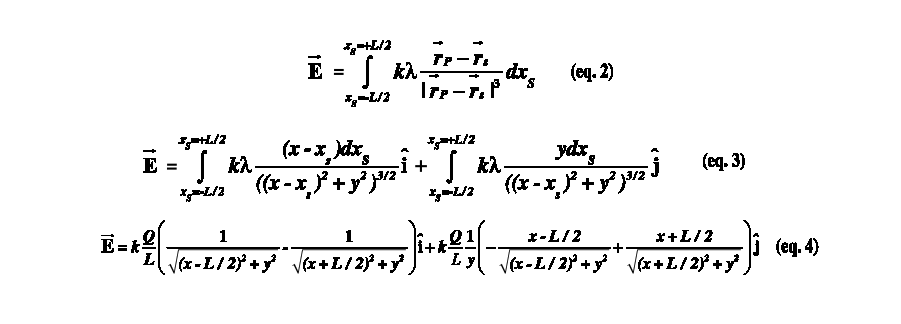

In the piece of code below we define the expression “rodField”, which  performs the integral in (eg. 2), resulting in (eq. 4). Recall that dq = lambda dx. Because the Integrate[] function incorporates the dx, we only use lambda = Q/L = 10^-9 C/m as the third argument of the eFieldFunc[].

rodCharge = 2* 10^(-9) (* C *)
rodLength = 2 (* m *)
lambda = rodCharge/rodLength (* linear charge density C/m^3 *)
rodField=
Integrate[
eFieldFunc[{xs,0},{x,y},lambda], 
{xs,-1,1},
Assumptions→(Element[x,Reals] && Element[y,Reals] && y!=0 && x!=0)
]

1/500000000

2

1/1000000000

{-(9 (√(1-2 x+x^2+y^2)-√(1+2 x+x^2+y^2)))/(√(1-2 x^2+x^4+2 y^2+2 x^2 y^2+y^4)),(9 (√(1-2 x+x^2+y^2)+x √(1-2 x+x^2+y^2)+√(1+2 x+x^2+y^2)-x √(1+2 x+x^2+y^2)))/(y √(1-2 x^2+x^4+2 y^2+2 x^2 y^2+y^4))}

Note 1: The length of the rod is L = 2, therefore the variable of integration xs is between -1 and 1. To indicate this we use {xs, -1, 1}.

Note 2: By default, Mathematica will assume that we are integrating complex variable. To tell Mathematica that that x and y are real and nonzero numbers we need to type after the last argument of the function Integrate[]:

 “Assumptions → (Element[x,Reals] && Element[y,Reals] && y!=0 && x!=0)”

which we do with the “Assumptions” option:

Note 3:  The line above between quotes is called an “option”. “Options” are like arguments that we use in a function, except they always come after the arguments. The syntax is of the form:

“optionName → optionValue”  
   
Between the “optionName” and “optionValue” there is a little arrow. The option that we are using in the Integrate[] function is called “Assumptions”. The option value is given inside the parenthesis after the little red arrow: x and y are non zero and real numbers. 

An “option” will usually modify slightly the way things are computed or presented. You have already encountered an option in Lesson 1 when you used the function SliceVectorPlot3D[]:

 “VectorStyle→Arrowheads[.01]”

In SliceVectorPlot3D[], the “VectorStyle” option was needed to change the size of the arrows head from its default value to .01. The “optionName” was “VectorStyle” and the  “optionValue” was “Arrowheads[0.1]” .

Because we have calculated the electric field in the (x,y) plane we can use any of the graphic functions for 2D vectors, example VectorPlot[] and StreamPlot[]. We will plot the electric field lines using  StreamPlot[ ]. You are invited to plot the electric field vectors.

StreamPlot[rodField, {x,-2,2},{y,-2,2}]

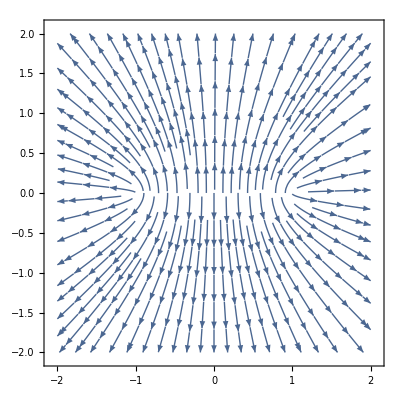

Problem 1 - Part A. Far away from the finite rod.
"Open/Close Section""Create Scratchpad""Save Work and Give Feedback"

Far a distance much larger than the length of the rod L, the rod’s electric field behaves as the electric field of a point charge. Propose a value of L for which the electric field pattern produced by the rod resembles the electric field of a point charge. Note: We do not expect an exact answer, a plot or several  plots is enough to justify the value of L that you propose.

Work saved at Tue 20 Feb 2018 19:16:49

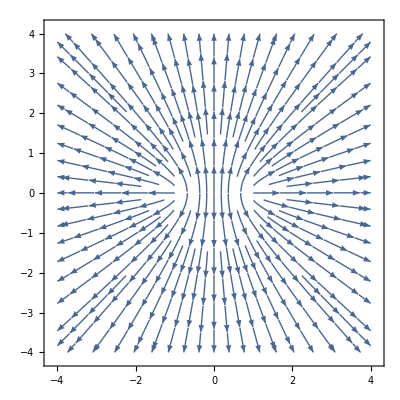

```mathematica
StreamPlot[rodField, {x,-4,4},{y,-4,4}]
```

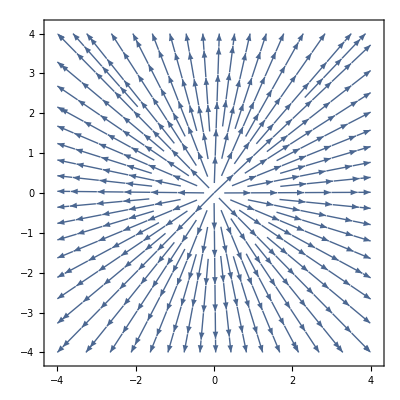

```mathematica
StreamPlot[eFieldFunc[{0,0},{x,y},rodCharge],{x,-4,4},{y,-4,4}]
```

From these two plots, it looks like the rod begins to behave like a point charge at radii greater than 2, maybe even a little closer.

Work saved at Tue 20 Feb 2018 19:29:32

```mathematica
rodLength = 0.5                          (* m *)
lambda = rodCharge/rodLength (* linear charge density C/m^3 *)
rodField05=
Integrate[
eFieldFunc[{xs,0},{x,y},lambda], 
{xs,-0.2,0.2},
Assumptions->(Element[x,Reals] && Element[y,Reals] && y!=0 && x!=0)
]
```

0.5

4.×10^-9

{-(180. (√(1.-10. x+25. x^2+25. y^2)-1. √(1.+10. x+25. x^2+25. y^2)))/(√(1.-10. x+25. x^2+25. y^2) √(1.+10. x+25. x^2+25. y^2)),(36. (√(1.-10. x+25. x^2+25. y^2)+5. x √(1.-10. x+25. x^2+25. y^2)+√(1.+10. x+25. x^2+25. y^2)-5. x √(1.+10. x+25. x^2+25. y^2)))/(y √(1.-10. x+25. x^2+25. y^2) √(1.+10. x+25. x^2+25. y^2))}

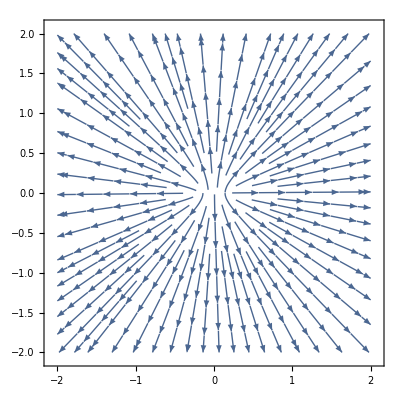

```mathematica
StreamPlot[rodField05, {x,-2,2},{y,-2,2}]
```

```mathematica
rodLength = 0.25                          (* m *)
lambda = rodCharge/rodLength (* linear charge density C/m^3 *)
rodField025=
Integrate[
eFieldFunc[{xs,0},{x,y},lambda], 
{xs,-0.2,0.2},
Assumptions->(Element[x,Reals] && Element[y,Reals] && y!=0 && x!=0)
]
```

0.25

8.×10^-9

{-(360. (√(1.-10. x+25. x^2+25. y^2)-1. √(1.+10. x+25. x^2+25. y^2)))/(√(1.-10. x+25. x^2+25. y^2) √(1.+10. x+25. x^2+25. y^2)),(72. (√(1.-10. x+25. x^2+25. y^2)+5. x √(1.-10. x+25. x^2+25. y^2)+√(1.+10. x+25. x^2+25. y^2)-5. x √(1.+10. x+25. x^2+25. y^2)))/(y √(1.-10. x+25. x^2+25. y^2) √(1.+10. x+25. x^2+25. y^2))}

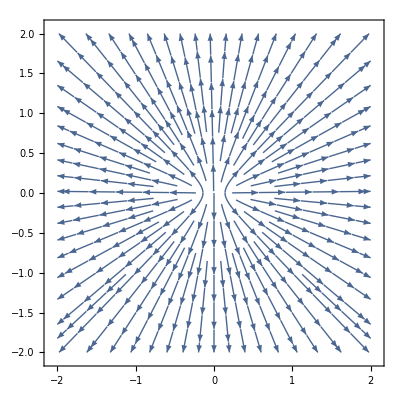

```mathematica
StreamPlot[rodField025, {x,-2,2},{y,-2,2}]
```

```mathematica
rodLength = 0.12                          (* m *)
lambda = rodCharge/rodLe25ngth (* linear charge density C/m^3 *)
rodField012=
Integrate[
eFieldFunc[{xs,0},{x,y},lambda], 
{xs,-0.2,0.2},
Assumptions->(Element[x,Reals] && Element[y,Reals] && y!=0 && x!=0)
]
```

0.12

1.66667×10^-8

{-(750. (√(1.-10. x+25. x^2+25. y^2)-1. √(1.+10. x+25. x^2+25. y^2)))/(√(1.-10. x+25. x^2+25. y^2) √(1.+10. x+25. x^2+25. y^2)),(150. (√(1.-10. x+25. x^2+25. y^2)+5. x √(1.-10. x+25. x^2+25. y^2)+√(1.+10. x+25. x^2+25. y^2)-5. x √(1.+10. x+25. x^2+25. y^2)))/(y √(1.-10. x+25. x^2+25. y^2) √(1.+10. x+25. x^2+25. y^2))}

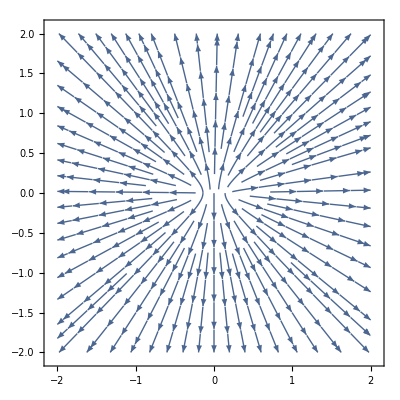

```mathematica
StreamPlot[rodField012, {x,-2,2},{y,-2,2}]
```

```mathematica
StreamPlot[eFieldFunc[{0,0},{x,y},rodCharge],{x,-4,4},{y,-4,4}]
```

-Graphics-

From these plots, it looks like the rod begins to behave like a point charge at length 0.12m, maybe even a little smaller.

After you view the teacher's solution, you can incorporate anything you learned into your work here if you would like to do so.

```mathematica
rodLength = 0.5                          (* m *)
lambda = rodCharge/rodLength (* linear charge density C/m^3 *)
rodField05=
Integrate[
eFieldFunc[{xs,0},{x,y},lambda], 
{xs,-0.2,0.2},
Assumptions->(Element[x,Reals] && Element[y,Reals] && y!=0 && x!=0)
]
```

0.5

4.×10^-9

{-(180. (√(1.-10. x+25. x^2+25. y^2)-1. √(1.+10. x+25. x^2+25. y^2)))/(√(1.-10. x+25. x^2+25. y^2) √(1.+10. x+25. x^2+25. y^2)),(36. (√(1.-10. x+25. x^2+25. y^2)+5. x √(1.-10. x+25. x^2+25. y^2)+√(1.+10. x+25. x^2+25. y^2)-5. x √(1.+10. x+25. x^2+25. y^2)))/(y √(1.-10. x+25. x^2+25. y^2) √(1.+10. x+25. x^2+25. y^2))}

```mathematica
StreamPlot[rodField05, {x,-2,2},{y,-2,2}]
```

-Graphics-

```mathematica
rodLength = 0.25                          (* m *)
lambda = rodCharge/rodLength (* linear charge density C/m^3 *)
rodField025=
Integrate[
eFieldFunc[{xs,0},{x,y},lambda], 
{xs,-0.2,0.2},
Assumptions->(Element[x,Reals] && Element[y,Reals] && y!=0 && x!=0)
]
```

0.25

8.×10^-9

{-(360. (√(1.-10. x+25. x^2+25. y^2)-1. √(1.+10. x+25. x^2+25. y^2)))/(√(1.-10. x+25. x^2+25. y^2) √(1.+10. x+25. x^2+25. y^2)),(72. (√(1.-10. x+25. x^2+25. y^2)+5. x √(1.-10. x+25. x^2+25. y^2)+√(1.+10. x+25. x^2+25. y^2)-5. x √(1.+10. x+25. x^2+25. y^2)))/(y √(1.-10. x+25. x^2+25. y^2) √(1.+10. x+25. x^2+25. y^2))}

```mathematica
StreamPlot[rodField025, {x,-2,2},{y,-2,2}]
```

-Graphics-

```mathematica
rodLength = 0.12                          (* m *)
lambda = rodCharge/rodLe25ngth (* linear charge density C/m^3 *)
rodField012=
Integrate[
eFieldFunc[{xs,0},{x,y},lambda], 
{xs,-0.2,0.2},
Assumptions->(Element[x,Reals] && Element[y,Reals] && y!=0 && x!=0)
]
```

0.12

1.66667×10^-8

{-(750. (√(1.-10. x+25. x^2+25. y^2)-1. √(1.+10. x+25. x^2+25. y^2)))/(√(1.-10. x+25. x^2+25. y^2) √(1.+10. x+25. x^2+25. y^2)),(150. (√(1.-10. x+25. x^2+25. y^2)+5. x √(1.-10. x+25. x^2+25. y^2)+√(1.+10. x+25. x^2+25. y^2)-5. x √(1.+10. x+25. x^2+25. y^2)))/(y √(1.-10. x+25. x^2+25. y^2) √(1.+10. x+25. x^2+25. y^2))}

```mathematica
StreamPlot[rodField012, {x,-2,2},{y,-2,2}]
```

-Graphics-

```mathematica
StreamPlot[eFieldFunc[{0,0},{x,y},rodCharge],{x,-4,4},{y,-4,4}]
```

-Graphics-

From these plots, it looks like the rod begins to behave like a point charge at length 0.12m, maybe even a little smaller.

Solution to Problem 1- Part A.
"Open/Close Section""Access Solution"

We will evaluate the integral to calculate the electric of the finite rod as done in the tutorial for different values of L = 0.4 m, 0.1 m, and 0.05 m. We will use StreamPlot[] to visualize each of the resulting fields.  

First: Consider the length L = 0.4 m. We will call the resulting field: rodField04

rodLength = 0.4                          (* m *)
lambda = rodCharge/rodLength (* linear charge density C/m^3 *)
rodField04=
Integrate[
eFieldFunc[{xs,0},{x,y},lambda], 
{xs,-0.2,0.2},
Assumptions→(Element[x,Reals] && Element[y,Reals] && y!=0 && x!=0)
]

StreamPlot[rodField04, {x,-2,2},{y,-2,2}]

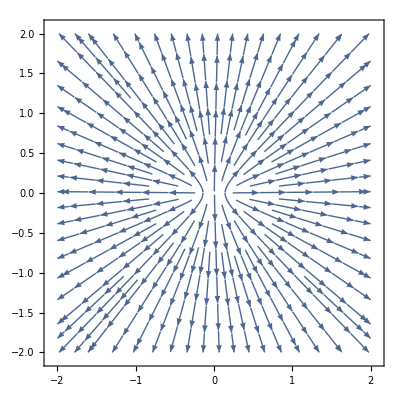

For  L = 0.4 m the electric field starts to look like the one of a point charge. We can still see the effects of the edges of the rod.

Second: Consider the length to be L = 0.1 m. We will call the resulting field: rodField01

rodLength = 0.1                          (* m *)
lambda = rodCharge/rodLength (* linear charge density C/m^3 *)
rodField01=
Integrate[
eFieldFunc[{xs,0},{x,y},lambda], 
{xs,-0.05,0.05},
Assumptions→(Element[x,Reals] && Element[y,Reals] && y!=0 && x!=0)
]

0.1

2.×10^-8

{-(3600. (√(1.-40. x+400. x^2+400. y^2)-1. √(1.+40. x+400. x^2+400. y^2)))/(√(1.-40. x+400. x^2+400. y^2) √(1.+40. x+400. x^2+400. y^2)),(180. (√(1.-40. x+400. x^2+400. y^2)+20. x √(1.-40. x+400. x^2+400. y^2)+√(1.+40. x+400. x^2+400. y^2)-20. x √(1.+40. x+400. x^2+400. y^2)))/(y √(1.-40. x+400. x^2+400. y^2) √(1.+40. x+400. x^2+400. y^2))}

StreamPlot[rodField01, {x,-2,2},{y,-2,2}]

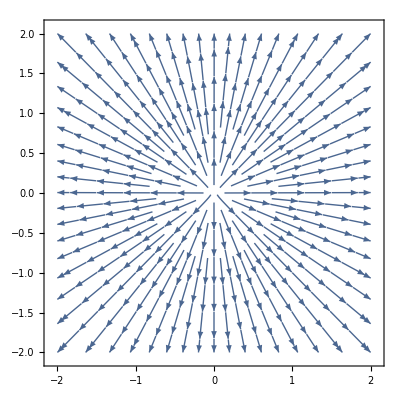

The electric field of a rod of length L = 0.1 m is similar to the one of a point charge.  

Third: Consider the length to be L = 0.05 m. We will call the resulting field: rodField005

rodLength = 0.05                          (* m *)
lambda = rodCharge/rodLength (* linear charge density C/m^3 *)
rodField005=
Integrate[
eFieldFunc[{xs,0},{x,y},lambda], 
{xs,-0.025,0.025},
Assumptions→(Element[x,Reals] && Element[y,Reals] && y!=0 && x!=0)
]

StreamPlot[rodField005, {x,-2,2},{y,-2,2}]

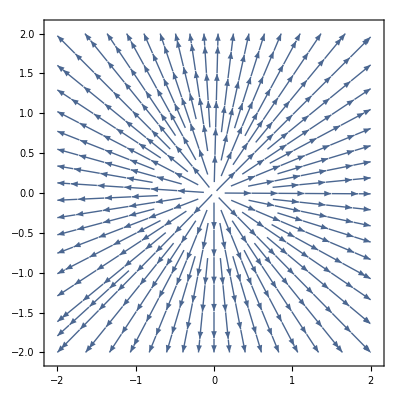

Use the button above to start viewing the solution

Problem 1- Part B: Electric field of an infinite rod of charge
"Open/Close Section""Create Scratchpad""Save Work and Give Feedback"

Calculate and visualize the electric field due to an infinite wire uniformly charged with a linear charge density lambda = 10^-10  C/m.

Here is how to say “infinity” in the Wolfram Language:

Infinity

∞

Here are some examples that involve  “Infinity”:

Limit[1/x, x→Infinity]

Limit[1/x, x→0]

Work saved at Tue 20 Feb 2018 19:21:23

```mathematica
lambda = 10^(-10) (* linear charge density C/m^3 *)
rodField2=
Integrate[
eFieldFunc[{xs,0},{x,y},lambda], 
{xs,-Infinity,Infinity},
Assumptions->(Element[x,Reals] && Element[y,Reals] && y!=0 && x!=0)
]
```

1/10000000000

{0,9/(5 y)}

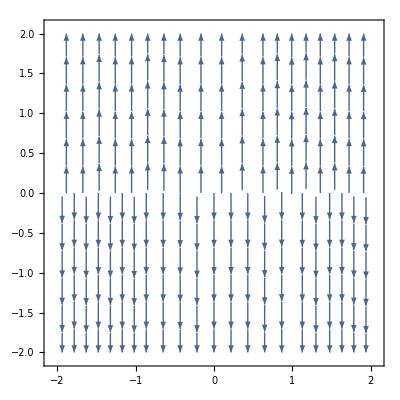

```mathematica
StreamPlot[rodField2, {x,-2,2},{y,-2,2}]
```

After you view the teacher's solution, you can incorporate anything you learned into your work here if you would like to do so.

```mathematica
lambda = 10^(-10) (* linear charge density C/m^3 *)
rodField2=
Integrate[
eFieldFunc[{xs,0},{x,y},lambda], 
{xs,-Infinity,Infinity},
Assumptions->(Element[x,Reals] && Element[y,Reals] && y!=0 && x!=0)
]
```

1/10000000000

{0,9/(5 y)}

```mathematica
StreamPlot[rodField2, {x,-2,2},{y,-2,2}]
```

-Graphics-

Solution to Problem 1- Part B
"Open/Close Section""Access Solution"

All we have to do is change the limits of integration from {xs,-1, 1} to {xs,-Infinity,Infinity}:

infiniteRodField=Integrate[eFieldFunc[{xs,0},{x,y},10^(-10)],{xs,-Infinity,Infinity},Assumptions→(Element[x,Reals]&&Element[y,Reals]&&y!=0 && x!=0)]

{0,9/(5 y)}

StreamPlot[infiniteRodField, {x,-2,2},{y,-2,2}]

-Graphics-

Use the button above to start viewing the solution

Problem 1 - Part C: Calculate the electric field of the finite rod at point P={1,2,3}
"Open/Close Section""Create Scratchpad""Save Work and Give Feedback"

Consider the wire of part A. It has a length L = 2 m and a charge Q = 2.10^-9 C uniformly distributed . The wire is in the x-axis centered at the origin of the coordinate system. Calculate the electric field at the point P = {1,2,3} created by a charged wire. ( Note that ‘rodField’ is a 2D vector field, not the 3D field.)

Note: You might find useful the function ReplaceAll[ ].
In the example below, the expression “w” depends on x, y, and z. The function ReplaceAll[] is replacing x by 1, y by 2 ans z by -1 in the expression of w:

w=x^2+2*y+z

x^2+2 y+z

ReplaceAll[w,{x→1,y→2,z→-1}]

4

Work saved at Tue 20 Feb 2018 19:35:18

```mathematica
rodLength = 0.4                          (* m *)
lambda = rodCharge/rodLength (* linear charge density C/m^3 *)
rodField04=
Integrate[
eFieldFunc[{xs,0, 0},{x,y,z},lambda], 
{xs,-0.2,0.2},
Assumptions->(Element[x,Reals] && Element[y,Reals] && Element[z,Reals] && y!=0 && x!=0&& z!=0)
]
```

0.4

5.×10^-9

{-(225. (√(1.-10. x+25. x^2+25. y^2+25. z^2)-1. √(1.+10. x+25. x^2+25. y^2+25. z^2)))/(√((1.-10. x+25. x^2+25. y^2+25. z^2) (1.+10. x+25. x^2+25. y^2+25. z^2))),(45. y (√(1.-10. x+25. x^2+25. y^2+25. z^2)+5. x √(1.-10. x+25. x^2+25. y^2+25. z^2)+√(1.+10. x+25. x^2+25. y^2+25. z^2)-5. x √(1.+10. x+25. x^2+25. y^2+25. z^2)))/((y^2+z^2) √(1.-10. x+25. x^2+25. y^2+25. z^2) √(1.+10. x+25. x^2+25. y^2+25. z^2)),(45. z (√(1.-10. x+25. x^2+25. y^2+25. z^2)+5. x √(1.-10. x+25. x^2+25. y^2+25. z^2)+√(1.+10. x+25. x^2+25. y^2+25. z^2)-5. x √(1.+10. x+25. x^2+25. y^2+25. z^2)))/((y^2+z^2) √(1.-10. x+25. x^2+25. y^2+25. z^2) √(1.+10. x+25. x^2+25. y^2+25. z^2))}

```mathematica
ReplaceAll[{-((225. (√(1.-10. x+25. x^2+25. y^2+25. z^2)-1. √(1.+10. x+25. x^2+25. y^2+25. z^2)))/(√((1.-10. x+25. x^2+25. y^2+25. z^2) (1.+10. x+25. x^2+25. y^2+25. z^2)))),(45. y (√(1.-10. x+25. x^2+25. y^2+25. z^2)+5. x √(1.-10. x+25. x^2+25. y^2+25. z^2)+√(1.+10. x+25. x^2+25. y^2+25. z^2)-5. x √(1.+10. x+25. x^2+25. y^2+25. z^2)))/((y^2+z^2) √(1.-10. x+25. x^2+25. y^2+25. z^2) √(1.+10. x+25. x^2+25. y^2+25. z^2)),(45. z (√(1.-10. x+25. x^2+25. y^2+25. z^2)+5. x √(1.-10. x+25. x^2+25. y^2+25. z^2)+√(1.+10. x+25. x^2+25. y^2+25. z^2)-5. x √(1.+10. x+25. x^2+25. y^2+25. z^2)))/((y^2+z^2) √(1.-10. x+25. x^2+25. y^2+25. z^2) √(1.+10. x+25. x^2+25. y^2+25. z^2))},{x->1, y->2,z->3}]
```

{0.342328,0.686612,1.02992}

Work saved at Tue 20 Feb 2018 19:42:01

```mathematica
rodCharge = 2* 10^(-9) (* C *)
rodLength = 2 (* m *)
lambda = rodCharge/rodLength (* linear charge density C/m^3 *)
rodField2=
Integrate[
eFieldFunc[{xs,0,0},{x,y,z},lambda], 
{xs,-1,1},
Assumptions->(Element[x,Reals] && Element[y,Reals] && Element[z,Reals] && y!=0 && x!=0 && z≠0)
]
```

1/500000000

2

1/1000000000

{-(9 (√(1-2 x+x^2+y^2+z^2)-√(1+2 x+x^2+y^2+z^2)))/(√((1+(-2+x) x+y^2+z^2) (1+x (2+x)+y^2+z^2))),(9 y (√(1-2 x+x^2+y^2+z^2)+x √(1-2 x+x^2+y^2+z^2)+√(1+2 x+x^2+y^2+z^2)-x √(1+2 x+x^2+y^2+z^2)))/((y^2+z^2) √((1+(-2+x) x+y^2+z^2) (1+x (2+x)+y^2+z^2))),(9 z (√(1-2 x+x^2+y^2+z^2)+x √(1-2 x+x^2+y^2+z^2)+√(1+2 x+x^2+y^2+z^2)-x √(1+2 x+x^2+y^2+z^2)))/((y^2+z^2) √((1+(-2+x) x+y^2+z^2) (1+x (2+x)+y^2+z^2)))}

```mathematica
ReplaceAll[rodField2,{x->1, y->2,z->3}]
```

{-(9 (√13-√17))/(√221),36/(13 √17),54/(13 √17)}

```mathematica
N[ReplaceAll[rodField2, {x->1,y->2, z->3}]]
```

{0.31333,0.671637,1.00746}

After you view the teacher's solution, you can incorporate anything you learned into your work here if you would like to do so.

```mathematica
rodCharge = 2* 10^(-9) (* C *)
rodLength = 2 (* m *)
lambda = rodCharge/rodLength (* linear charge density C/m^3 *)
rodField2=
Integrate[
eFieldFunc[{xs,0,0},{x,y,z},lambda], 
{xs,-1,1},
Assumptions->(Element[x,Reals] && Element[y,Reals] && Element[z,Reals] && y!=0 && x!=0 && z≠0)
]
```

1/500000000

2

1/1000000000

{-(9 (√(1-2 x+x^2+y^2+z^2)-√(1+2 x+x^2+y^2+z^2)))/(√((1+(-2+x) x+y^2+z^2) (1+x (2+x)+y^2+z^2))),(9 y (√(1-2 x+x^2+y^2+z^2)+x √(1-2 x+x^2+y^2+z^2)+√(1+2 x+x^2+y^2+z^2)-x √(1+2 x+x^2+y^2+z^2)))/((y^2+z^2) √((1+(-2+x) x+y^2+z^2) (1+x (2+x)+y^2+z^2))),(9 z (√(1-2 x+x^2+y^2+z^2)+x √(1-2 x+x^2+y^2+z^2)+√(1+2 x+x^2+y^2+z^2)-x √(1+2 x+x^2+y^2+z^2)))/((y^2+z^2) √((1+(-2+x) x+y^2+z^2) (1+x (2+x)+y^2+z^2)))}

```mathematica
ReplaceAll[rodField2,{x->1, y->2,z->3}]
```

{-(9 (√13-√17))/(√221),36/(13 √17),54/(13 √17)}

```mathematica
N[ReplaceAll[rodField2, {x->1,y->2, z->3}]]
```

{0.31333,0.671637,1.00746}

solution to Problem 1 - Part C
"Open/Close Section""Access Solution"

We will calculate the three components of the electric field at a generic point {x,y,x}, following the same steps shown in the tutorial to calculate the 2D expression of the electric field of a finite rod. Then we will evaluate the components at the particular point P = {1,2,3}.

rodCharge = 2* 10^(-9) (* C *)
rodLength = 2 (* m *)
lambda = rodCharge/rodLength (* linear charge density C/m^3 *)
rodField3D=
Integrate[
eFieldFunc[{xs,0,0},{x,y,z},lambda], 
{xs,-1,1},
Assumptions→(Element[x,Reals] && Element[y,Reals] && Element[z,Reals] && y!=0 && x!=0 && z≠0)
]

1/500000000

2

1/1000000000

{-(9 (√(1-2 x+x^2+y^2+z^2)-√(1+2 x+x^2+y^2+z^2)))/(√((1+(-2+x) x+y^2+z^2) (1+x (2+x)+y^2+z^2))),(9 y (√(1-2 x+x^2+y^2+z^2)+x √(1-2 x+x^2+y^2+z^2)+√(1+2 x+x^2+y^2+z^2)-x √(1+2 x+x^2+y^2+z^2)))/((y^2+z^2) √((1+(-2+x) x+y^2+z^2) (1+x (2+x)+y^2+z^2))),(9 z (√(1-2 x+x^2+y^2+z^2)+x √(1-2 x+x^2+y^2+z^2)+√(1+2 x+x^2+y^2+z^2)-x √(1+2 x+x^2+y^2+z^2)))/((y^2+z^2) √((1+(-2+x) x+y^2+z^2) (1+x (2+x)+y^2+z^2)))}

Now we can evaluate the field where we need to, by plugging in the numbers for x, y and z using ReplaceAll[]

ReplaceAll[rodField3D,{x→1, y→2,z→3}]

{-(9 (√13-√17))/(√221),36/(13 √17),54/(13 √17)}

Note 1: To obtain the answer to the problem directly we can use as input to the eFiledFunc[]  the value {1,2,3} instead of {x,y,z}.  
Note 2: The function ReplaceAll[ ] takes a list of “rules” like “a -> b” and substitutes “b” in for “a” everywhere in an expression (everywhere in rodField3D, in this case)

Note 3:  Mathematica tries to return exact answers when possible. This is shown in the result of the electric field at point P where we see square roots of prime numbers.  If you need a decimal (actually “machine-precision number”) version of any expression, you can use the N[ ] function:

N[ReplaceAll[rodField3D,{x→1, y→2,z→3}]

```mathematica
N[ReplaceAll[rodField3D,{x->1, y->2,z->3}]]
```

{0.31333,0.671637,1.00746}

Use the button above to start viewing the solution